## Cell Automata (1: elongating tip)

```mathematica
(*0->ecad,1->brachyury,-1->ecad/brach*)
```

```mathematica
0.005+0.01+0.985
```

1.

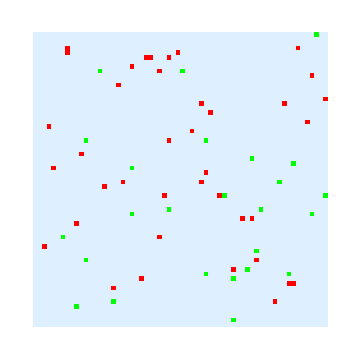

```mathematica
(boardC=RandomChoice[ {0.005,0.01,0.985}-> {0,1,-1},{64,64}])//ArrayPlot[#,
ColorRules->{1->Red, 0 -> Green, -1->LightBlue},ImageSize->Medium,PlotRange->All]&
```

```mathematica
(*func[list_]:=Module[{cell=list[[2,2]],flat=Union@Flatten[list]},
If[ MemberQ[flat,0]~And~MemberQ[flat,-1],
RandomChoice[{0.80,0.15,0.05}->{0,-1,1}],
RandomChoice[{0.05,0.95}->{-1,1}]]
];*)
```

```mathematica
Clear[func];
func[list_]:=Module[{cell=list[[2,2]],flat=Union@Flatten[list]},
Which[ 
MemberQ[flat,0],
RandomChoice[{0.70,0.10,0.20}->{0,-1,1}],
 True,
1]
];
```

```mathematica
cellularAutomaton[board_,steps_]:=CellularAutomaton[{func[#]&,{},{1,1}},board,{{{steps}}}]
```

```mathematica
plot=ArrayPlot[#,ColorRules->{ 0 ->Green,-1->LightBlue,1->Red},ImageSize->Medium]&;
```

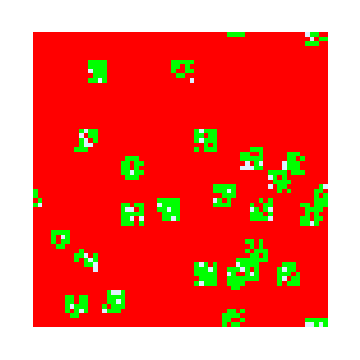

```mathematica
(array=cellularAutomaton[boardC,2])//plot
```

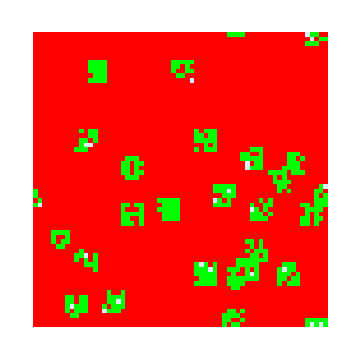

```mathematica
(arrayMod=Nest[#/.(-1 :>RandomChoice[{0,1,-1}])&,array,1])//plot
```

```mathematica
TableForm[Counts@Flatten[#]&/@{array,arrayMod}]
```

<|1→3652,0→384,-1→60|>
<|1→3673,0→401,-1→22|>

```mathematica
Style["Ecadherin/Brachyury cells prior: "~~ToString[Counts[Flatten[array]][-1]],Bold]
Style["Ecadherin/Brachyury cells after: "~~ToString[Counts[Flatten[arrayMod]][-1]],Bold]
```

Ecadherin/Brachyury cells prior: 60

Ecadherin/Brachyury cells after: 22

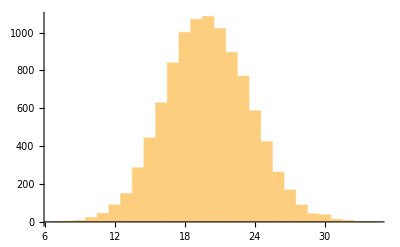

```mathematica
DeleteMissing[Table[Counts[Flatten@Nest[#/.(-1 :>RandomChoice[{0,1,-1}])&,array,1]][-1],{10000}]]//Histogram
```

## Cell Automata (2 : non elongating tip)

```mathematica
(*0->ecad,1->brachyury,-1->ecad/brach*)
```

```mathematica
0.0025+0.0125+0.985
```

1.

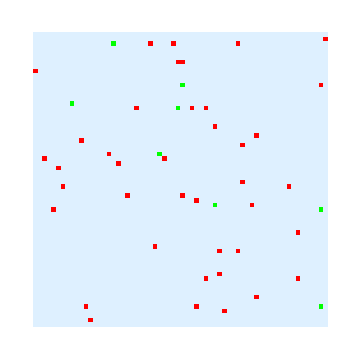

```mathematica
(board=RandomChoice[ {0.0025,0.0125,0.985}-> {0,1,-1},{64,64}])//ArrayPlot[#,
ColorRules->{1->Red, 0 -> Green, -1->LightBlue},ImageSize->Medium,PlotRange->All]&
```

```mathematica
(*func[list_]:=Module[{cell=list[[2,2]],flat=Union@Flatten[list]},
If[ MemberQ[flat,0]~And~MemberQ[flat,-1],
RandomChoice[{0.80,0.15,0.05}->{0,-1,1}],
RandomChoice[{0.05,0.95}->{-1,1}]]
];*)
```

```mathematica
Clear[func];
func[list_]:=Module[{cell=list[[2,2]],flat=Union@Flatten[list]},
Which[ 
MemberQ[flat,0],
RandomChoice[{0.70,0.10,0.20}->{0,-1,1}],
 True,
1]
];
```

```mathematica
cellularAutomaton[board_,steps_]:=CellularAutomaton[{func[#]&,{},{1,1}},board,{{{steps}}}]
```

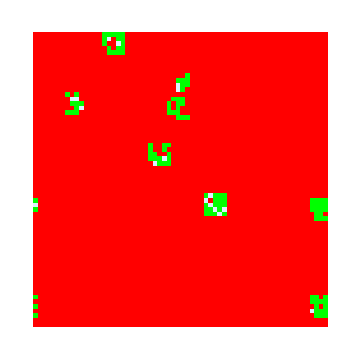

```mathematica
(array2=cellularAutomaton[board,2])//ArrayPlot[#,ColorRules->{ 0 ->Green,-1->LightBlue,1->Red},ImageSize->Medium]&
```

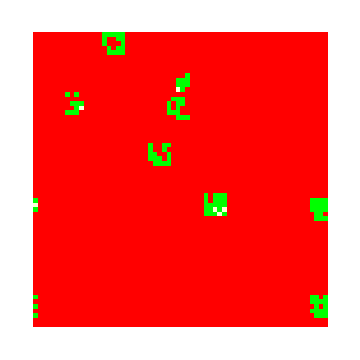

```mathematica
(array2m=Nest[#/.(-1 :>RandomChoice[{0,1,-1}])&,array2,1])//ArrayPlot[#,ColorRules->{ 0 ->Green,-1->LightYellow,1->Red},ImageSize->Medium]&
```

```mathematica
TableForm[Counts@Flatten[#]&/@{array2,array2m}]
```

<|1→3962,0→117,-1→17|>
<|1→3968,0→122,-1→6|>

```mathematica
Style["Ecadherin/Brachyury cells prior: "~~ToString[Counts[Flatten[array2]][-1]],Bold]
Style["Ecadherin/Brachyury cells after: "~~ToString[Counts[Flatten[array2m]][-1]],Bold]
```

Ecadherin/Brachyury cells prior: 17

Ecadherin/Brachyury cells after: 6

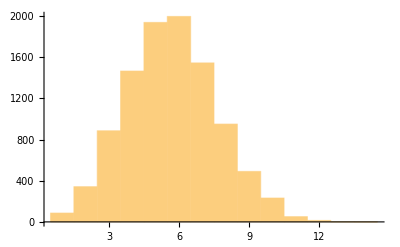

```mathematica
DeleteMissing[Table[Counts[Flatten@Nest[#/.(-1 :>RandomChoice[{0,1,-1}])&,array2,1]][-1],{10000}]]//Histogram
```

## ABM

```mathematica
(*create a board*)
```

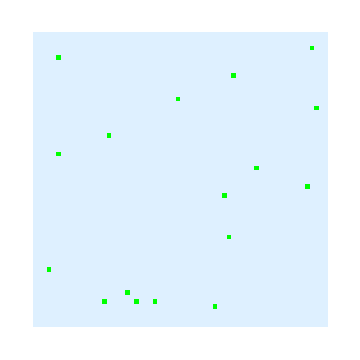

```mathematica
(board=RandomChoice[ {0.004,0.996}->{0,1},{64,64}])//ArrayPlot[#,ColorRules->{1->LightBlue, 0 -> Green},ImageSize->Medium,PlotRange->All]&
```

```mathematica
With[{pos=Flatten[MapIndexed[#2&,board,{2}],1]},
With[{nearestFunc=Nearest[pos]},
func[board_]:=Block[{assoc,ecadseeds,ecadseedNeigh,posTomodify,update1,update2},
assoc=AssociationThread[pos->Flatten[board]];
ecadseeds=SparseArray[(1-Unitize[board])]["NonzeroPositions"];
ecadseedNeigh=Flatten[nearestFunc[#,{18,2}]&/@ecadseeds,1];
posTomodify=Pick[ecadseedNeigh,Lookup[assoc,ecadseedNeigh],1];
update1=Thread[#-> RandomChoice[{0.90,0.025,0.075}->{0,1,-1},Length[#]]]&@posTomodify;
AssociateTo[assoc,update1];
update2=Thread[#->RandomChoice[{0.3255,0.672,0.00025}-> {1,-1,0},Length[#]]]&[Complement[Keys@Select[assoc,#==1&],posTomodify]];
AssociateTo[assoc,update2];
Normal@SparseArray[Normal@assoc]
];
];
];
```

```mathematica
fixedptSoln=FixedPointList[func,board];
ListAnimate[MatrixPlot[#,ColorRules->{0-> Green,1->LightBlue,-1->Red}]&/@fixedptSoln,SaveDefinitions->True]
```

```mathematica
MorphologicalComponents[(1-Unitize[SparseArray[Last@fixedptSoln]]),CornerNeighbors->True]//Colorize//Image[#,ImageSize->Small]&
```

-Graphics-

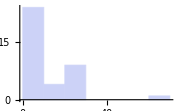

```mathematica
ComponentMeasurements[MorphologicalComponents[(1-Unitize[SparseArray[Last@fixedptSoln]]),CornerNeighbors->True],"Count"]//Values//Histogram[#,PlotTheme->"Classic",
ImageSize->Small]&
```